```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-70_phon_dos"];
phDOSfiles={"1.total_dos.dat","2.total_dos.dat","3.total_dos.dat","4.total_dos.dat","5.total_dos.dat","6.total_dos.dat","7.total_dos.dat","8.total_dos.dat","9.total_dos.dat","10.total_dos.dat","11.total_dos.dat"};
fren70dos=Table[ReadList[phDOSfiles[[i]],{Number,Number}],{i,1,Length@phDOSfiles}];
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/perf_phon_dos"];
perf=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{30,0.0},{32,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-1126_phon_dos"];
fren1126=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{30,0.0},{32,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-129_phon_dos"];
fren129=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{30,0.0},{32,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-142_phon_dos"];
fren142=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{30,0.0},{32,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-174_phon_dos"];
fren174=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{30,0.0},{32,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-70_phon_dos"];
fren70=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{30,0.0},{32,0.0}}}],2],{i,1,Length@phDOSfiles}];
```

```mathematica
names={"perf","fren129","fren142","fren70","fren174","fren1126"};
objects={perf,fren129,fren142,fren70,fren174,fren1126};
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850,4.875,4.900};
vols=(alatts*2)^3/64;
```

```mathematica
fren1126Data=Table[Table[Flatten[{fren1126[[j]][[i]][[1]],vols[[j]],fren1126[[j]][[i]][[2]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
fren1126Data2D=Table[Table[Flatten[{fren1126[[j]][[i]][[1]],fren1126[[j]][[i]][[2]]+10*vols[[j]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
```

```mathematica
data=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]],vols[[j]],objects[[k]][[j]][[i]][[2]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
```

```mathematica
data2D=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]],objects[[k]][[j]][[i]][[2]]+10*vols[[j]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
```

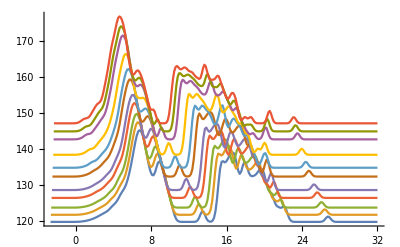

```mathematica
ListPointPlot3D@fren1126Data;
ListLinePlot@fren1126Data2D
```

```mathematica
2
```

2

#### Plot3d

```mathematica
plotStyle3D={BoxRatios->{1,1,1},FillingStyle->Directive[Thickness[1],Orange,Thin,Opacity[0.1]],Filling->Bottom,PlotTheme->"Scientific",AxesLabel->{Style["ω (THz)",18,Black],Style["Volume \n(Å^3/atom) ",18,Black],Style["DOS ",18,Black]" \n(1/THz)  "},AxesStyle->Directive[18,Black,Thickness[0.004]],Boxed->False,BoxStyle->Directive[Thickness[0.00001],Dashing[0.02]],PlotStyle->Directive[Black,PointSize[0.006]],ImageSize->650,ViewPoint->{-5005,-100000,15}};
ListPointPlot3D[fren1126Data,Evaluate@plotStyle3D]/.Point[a___]:>{Thickness[0.004],Line[a]};
```

#### Plot2D

```mathematica
plotStyle={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,None},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS ",18,Black]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->450,PlotRange->{{0,30},Automatic}};
```

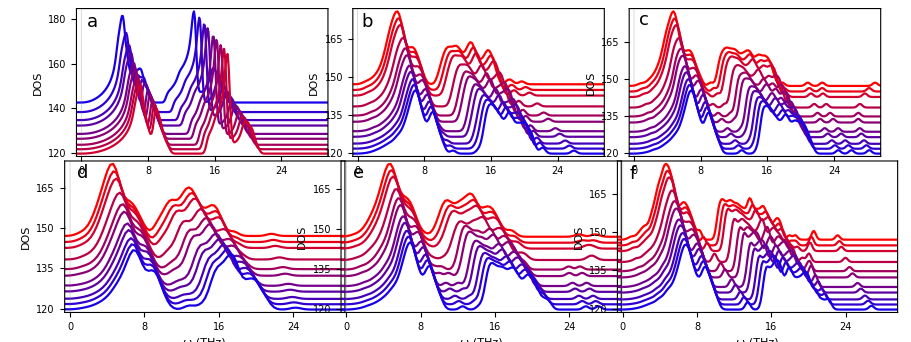

```mathematica
plotStyle1={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS ",18,Black]},PlotStyle->Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Reverse@Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,29},Automatic},PlotLabels->{Placed[Style["a",18,Black],{0.09,0.88}]}};




plotStyle2={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,29},Automatic},PlotLabels->{Placed[Style["b",18,Black],{0.113,0.86}]}};
plotStyle3={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,29},Automatic},PlotLabels->{Placed[Style["c",18,Black],{0.128,0.88}]}};
plotStyle4={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS ",18,Black]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->390,PlotRange->{{0,29},Automatic},PlotLabels->{Placed[Style["d",18,Black],{0.106,0.87}]}};


plotStyle5={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->390,PlotRange->{{0,29},Automatic},PlotLabels->{Placed[Style["e",18,Black],{0.13,0.88}]}};
plotStyle6={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->390,PlotRange->{{0,29},Automatic},PlotLabels->{Placed[Style["f",18,Black],{0.1,0.87}]}};
plotStyles={plotStyle1,plotStyle2,plotStyle3,plotStyle4,plotStyle5,plotStyle6};

plots=Table[ListLinePlot[Reverse@data2D[[i]],Evaluate@plotStyles[[i]]],{i,1,6}];
gridplot=GraphicsGrid[{plots[[1;;3]],plots[[4;;6]]},Spacings->{-90,-30}]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/phon-dos.pdf",gridplot]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/phon-dos.pdf